```mathematica
Clear["Global`*"]
```

```mathematica
h[x_]= Piecewise[{{h0 a/(a+x),x>0},{h0,x≤ 0}}];
```

```mathematica
h0=2;a=2;
```

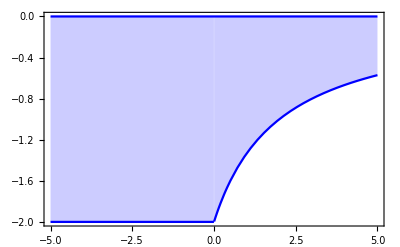

```mathematica
Plot[{-h[x],0},{x,-5,5},Frame->True,Axes->False,Filling->Axis,PlotStyle->{Blue,Blue}]
```

```mathematica
c[x_]= Sqrt[g h[x]]; g=9.8;
```

```mathematica
kx[x_]= Sqrt[ω^2/c[x]^2-ky^2];
```

```mathematica
ω=Sqrt[2 g h0];
ky=1;
```

```mathematica
ϕ[x_]= Integrate[kx[x1],{x1,0,x},Assumptions->x∈Reals]
```

Piecewise[{{x, x<0.}, {0.666667 (-1.+√(1.+x)+x √(1.+x)), x>0.}, {0., True}}]

```mathematica
z[x_,y_,t_]= 1/(c[x] Sqrt[kx[x]]) Exp[I (ky y + ϕ[x] - ω t)];
```

```mathematica
ListAnimate[Table[Plot[Re[z[x,0,t]],{x,-10,15},PlotRange->{-1/2,1/2}],{t,0,1.9Pi/ω,.1 Pi/ω}]]
```

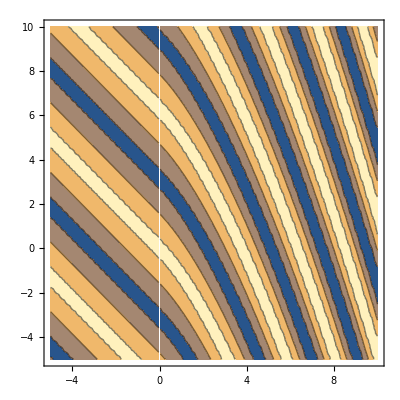
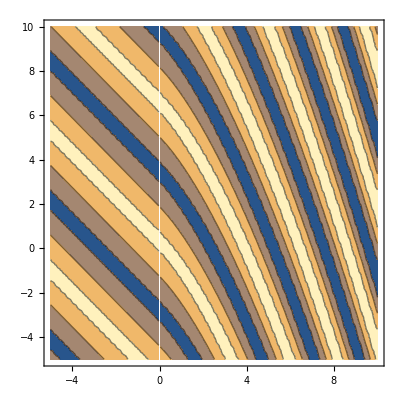
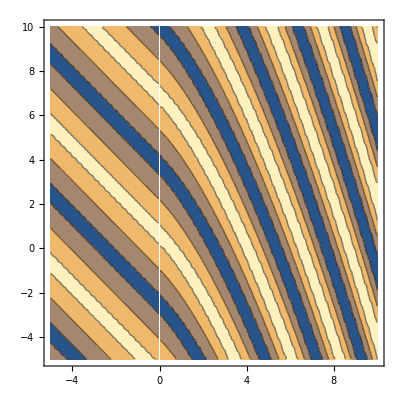
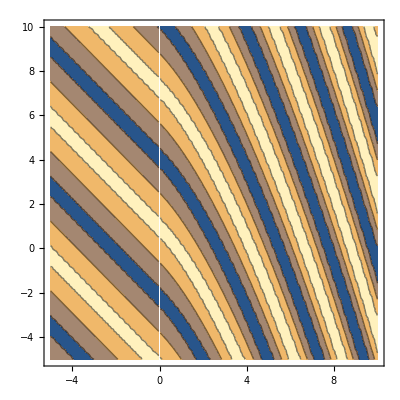
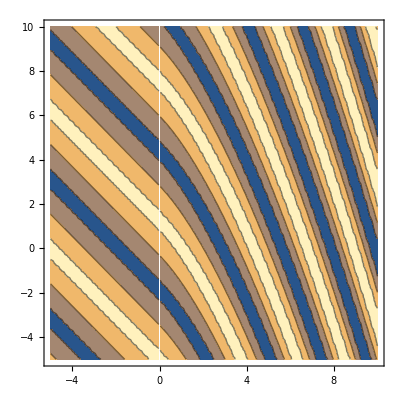
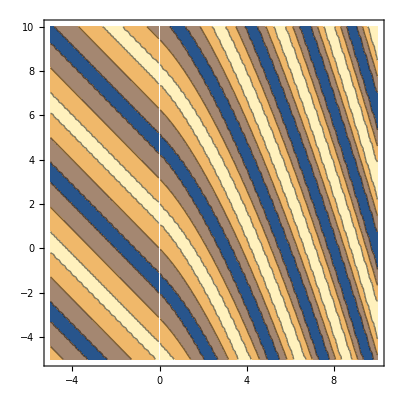
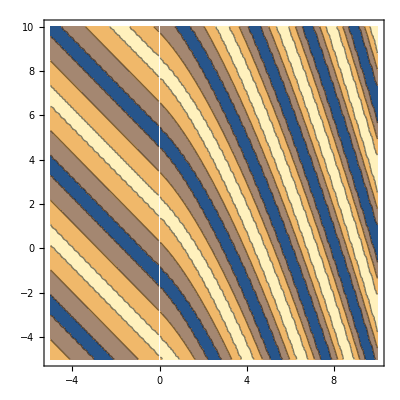
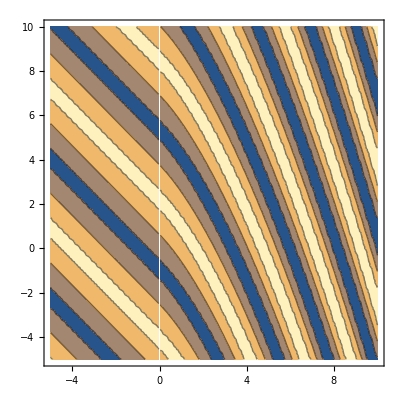

```mathematica
waves=Table[ContourPlot[Re[z[x,y,t]],{x,-5,10},{y,-5,10},PlotRange->{-1,1},PlotPoints->60,MaxRecursion->0],{t,0,1.9Pi/ω,.1Pi/ω}]
```

```mathematica
ListAnimate[waves]
```

```mathematica
Print/@waves;
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

«14 more identical outputs»

```mathematica
x0[n_]= -5;
y0[n_]= -7 + 4 n;
```

```mathematica
ray[n_]:= ray[n]={x,y}/.NDSolve[{x'[t]==c[x[t]]kx[x[t]]/Sqrt[ky^2+kx[x[t]]^2],
y'[t]==c[x[t]]ky/Sqrt[ky^2+kx[x[t]]^2],x[0]==x0[n],y[0]==y0[n]},{x,y},{t,0,10}][[1]]
```

```mathematica
plot[n_]:= ParametricPlot[{ray[n][[1]][t],ray[n][[2]][t]}//Evaluate,{t,0,10},PlotStyle->Red]
```

```mathematica
Show[Prepend[Table[plot[n],{n,-1,3}],waves[[1]]]]//Quiet
```

-Graphics-